# Deriving Percent Overshoot, Settling Time, and Other Performance Metrics

Christopher Lum
lum@uw.edu

This document accompanies the YouTube video at https://youtu.be/QWCLthgJEbc.

## Compute the Analytical Response of a 2nd Order System to a Step Input

```mathematica
(*Define transfer function*)
G[s_]=ωn^2/(s^2+2 ζ ωn s+ωn^2);

(*Compute R(s) (response to a step of magnitude A)*)
R[s_]=G[s] A/s;

(*Perform the inverse Laplace transfer to go back to time domain*)
yStep[t_]=Simplify[InverseLaplaceTransform[R[s],s,t],{ωn>0,ζ>0}]//Expand
```

-A/(-1+ζ^2)+(A ⅇ^(-t (ζ+√(-1+ζ^2)) ωn))/(2 (-1+ζ^2))+(A ⅇ^(2 t √(-1+ζ^2) ωn-t (ζ+√(-1+ζ^2)) ωn))/(2 (-1+ζ^2))+(A ζ^2)/(-1+ζ^2)-(A ⅇ^(-t (ζ+√(-1+ζ^2)) ωn) ζ^2)/(2 (-1+ζ^2))-(A ⅇ^(2 t √(-1+ζ^2) ωn-t (ζ+√(-1+ζ^2)) ωn) ζ^2)/(2 (-1+ζ^2))+(A ⅇ^(-t (ζ+√(-1+ζ^2)) ωn) ζ)/(2 √(-1+ζ^2))-(A ⅇ^(2 t √(-1+ζ^2) ωn-t (ζ+√(-1+ζ^2)) ωn) ζ)/(2 √(-1+ζ^2))

You can simplify/reduce this to the form of 

	y(t)=A+e^(-σ t)(a e^(-ω t)-b  e^(ω t))						(Eq.4)
	
where	a=((A ζ)/(2 √(ζ^2-1))-1/2 A  )
		b=(1/2 A+(A  ζ)/(2 √(ζ^2-1))) 
		σ=ζ ω_n
		ω=√(ζ^2-1)ω_n

```mathematica
yStepCheck[t_]=A+Exp[-σ t](a Exp[-ω t]-b Exp[ω t]);
```

```mathematica
(*Verify that ystep is the same as ystepcheck*)
```

```mathematica
yStep[t]==yStepCheck[t]/.{a->(A ζ)/(2 √(-1+ζ^2))-1/2 A,b->1/2 A+(A ζ)/(2 √(-1+ζ^2)),σ->ζ ωn,ω->√(ζ^2-1) ωn}//Simplify
```

True

Define the cos/sin representation of y(t)

```mathematica
yStepTrig[t_]=A-A Exp[-σ t] (Cos[ωd t]+ζ/(√(1-ζ^2))Sin[ωd t])/.{σ->ζ ωn,ωd->√(1-ζ^2) ωn}
```

A-A ⅇ^(-t ζ ωn) (Cos[t √(1-ζ^2) ωn]+(ζ Sin[t √(1-ζ^2) ωn])/(√(1-ζ^2)))

Verify that this satisfies the original 2nd order ODE

	y^(..)(t)+2 ζ ω_n ẏ(t)+ω_n^2 y(t)=ω_n^2 A

```mathematica
D[yStepTrig[t],{t,2}]+2 ζ ωn D[yStepTrig[t],t]+ωn^2 yStepTrig[t]==ωn^2 A//Simplify
```

True

Verify that this has zero initial conditions

```mathematica
yStepTrig[0]
D[yStepTrig[t],t]/.{t->0}
```

0

0

Visualize the function y(t)

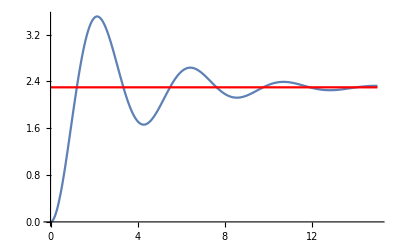

```mathematica
(*Chose specific values to use for plotting*)
Agiven=2.3;
ωngiven=1.5;
ζgiven=0.2;

tFinal = 15;

(*Plot the function*)
Show[
(*Show y(t)*)
Plot[yStepTrig[t]/.{A->Agiven,ζ->ζgiven, ωn->ωngiven},{t,0,tFinal},
PlotRange->All],

(*Show r(t)*)
Plot[A/.{A->Agiven},{t,0,tFinal},
PlotStyle->Red]
]
```

## Compute Performance Metrics for an Example System

Example

```mathematica
ωngiven
ζgiven
Agiven
```

1.5

0.2

2.3

```mathematica
Tp=π/(√(1-ζ^2)ωn)/.{A->Agiven,ζ->ζgiven,ωn->ωngiven}
```

2.13758

```mathematica
Mpt=A(1+Exp[-(π ζ)/(√(1-ζ^2))])/.{A->Agiven,ζ->ζgiven,ωn->ωngiven}
```

3.51123

```mathematica
PO=100 Exp[-(π ζ)/(√(1-ζ^2))]/.{A->Agiven,ζ->ζgiven,ωn->ωngiven}
```

52.6621

```mathematica
TsTilde=(-Log[δ])/(ζ ωn)/.{A->Agiven,ζ->ζgiven,ωn->ωngiven,δ->0.05}
```

9.98577